```mathematica
projectDir = "/Users/pwrzosek/Documents/GitHub/AvoidedQP/t-J_model";
PnDir ="./Pn/";
zDir="./z/";
SetDirectory[projectDir];
```

```mathematica
files=FileNames["*.txt",{PnDir,zDir}];
zFiles=Table[Table[Select[files,StringMatchQ[#,StringJoin["*z_L=",ToString[it],"_J=",s,"*.txt"]]&],{it,2,14,2}],{s,{"0.4","1.0"}}];
PnFiles=Table[Table[Select[files,StringMatchQ[#,StringJoin["*Pn_L=",ToString[it],"_J=",s,"*.txt"]]&],{it,2,14,2}],{s,{"0.4","1.0"}}];
```

```mathematica
PnDims=Dimensions[PnFiles];
PnData=Table[Import[PnFiles[[it,jt,lt]],"Table"],{it,PnDims[[1]]},{jt,PnDims[[2]]},{lt,PnDims[[3]]}];
zDims=Dimensions[zFiles];
zData=Table[Import[zFiles[[it,jt,lt]],"Table"],{it, zDims[[1]]},{jt,zDims[[2]]},{lt,zDims[[3]]}];
```

```mathematica
ns={2,4,6,8,10,12,14}
js=Table[DecimalForm[x,{1,1}],{x,{0.4,1.0}}]
ms=Table[DecimalForm[x,{1,1}],{x,0.0,1.0,0.1}]
```

{2,4,6,8,10,12,14}

{0.4,1.0}

{0.0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.0}

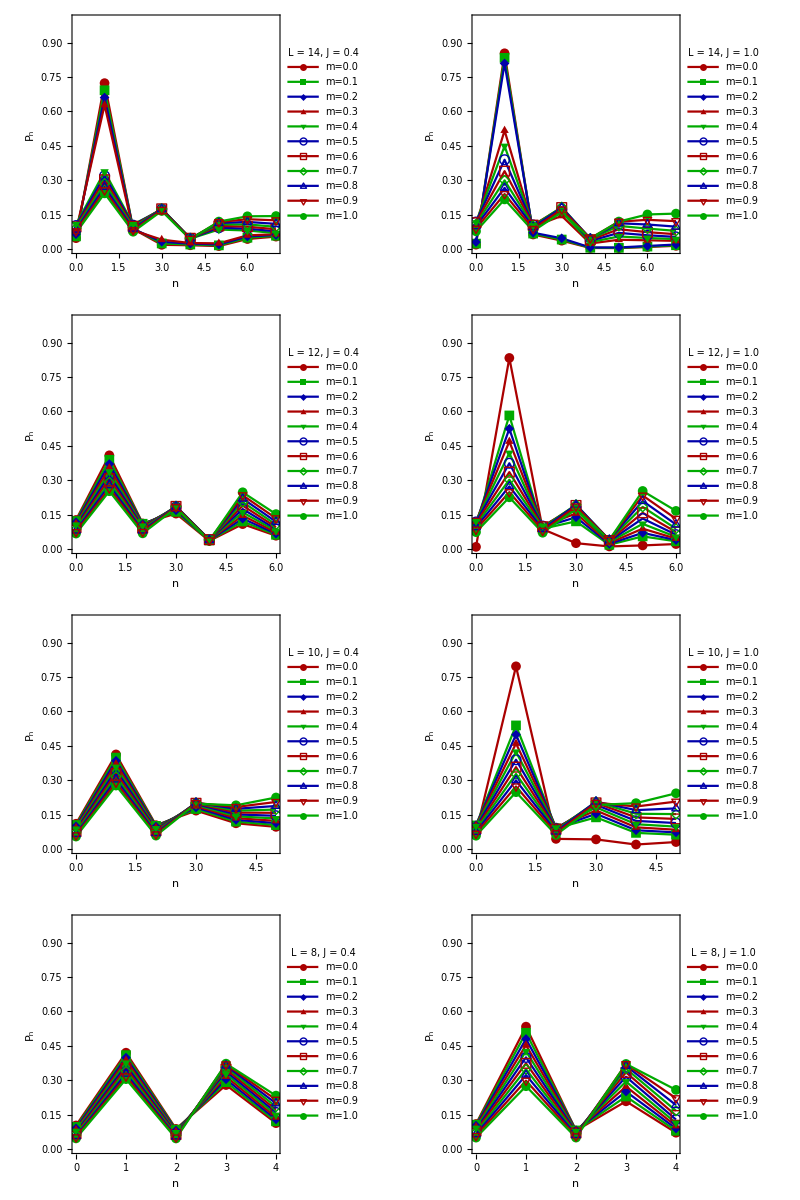

```mathematica
pnPlots=Grid[Table[ListLinePlot[Table[Table[{n-1,Flatten[PnData[[jt,it,lt]]][[n]]},{n,1+ns[[it]]/2}],{lt,PnDims[[3]]}],PlotRange->{0,1},Frame->True,Axes->False,PlotStyle->{Darker[Red],Darker[Green],Darker[Blue]},ImageSize->Large,FrameStyle->Directive[Black,18],PlotLegends->Placed[LineLegend[Table[StringTake[PnFiles[[jt,PnDims[[2]],lt]],{20,24}],{lt,PnDims[[3]]}],LegendLabel->StringJoin["L = ",ToString[ns[[it]]],",  J = ",ToString[js[[jt]]]],LegendLayout->{"Column",4}],{Right,Center}],AspectRatio->1/GoldenRatio,PlotMarkers->{Automatic, 10},FrameLabel->{"n","P_n"}],{it,PnDims[[2]],4,-1},{jt,PnDims[[1]]}]]
```

```mathematica
Export["./figs/Pn/Pn.png",pnPlots,ImageResolution->100]
```

./figs/Pn/Pn.png

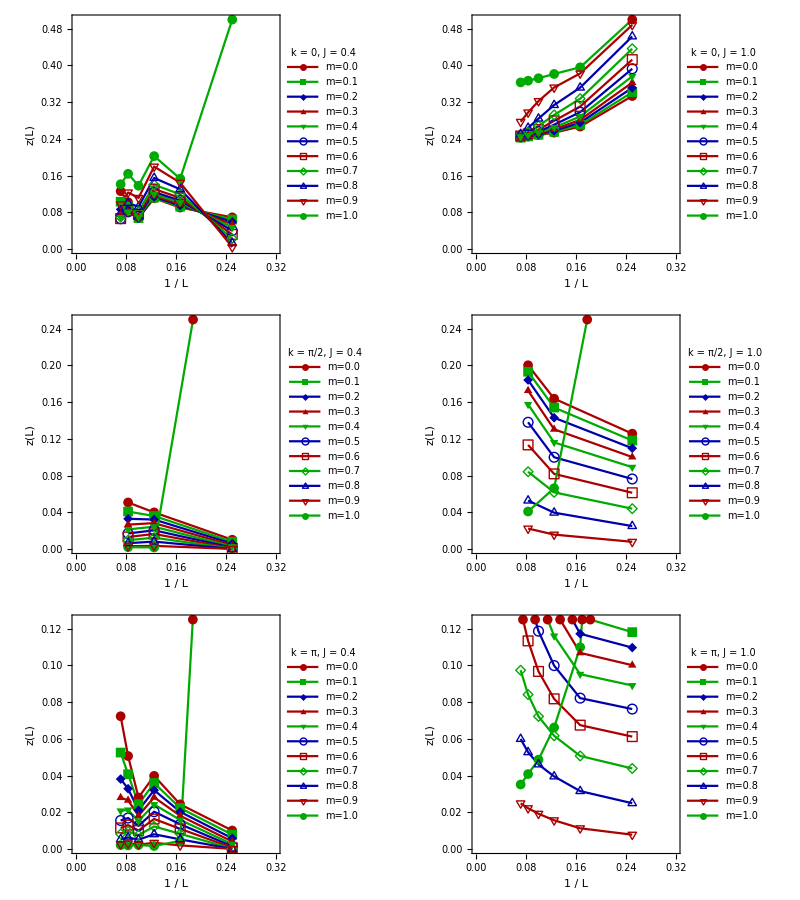

```mathematica
zPlots=Grid[{
Table[ListLinePlot[Table[Table[{1/ns[[in]],zData[[jt,in,im,1,2]]},{in,2,zDims[[2]]}],{im,zDims[[3]]}],PlotRange->{{0,.32},{0,0.5}},Frame->True,Axes->False,PlotStyle->{Darker[Red],Darker[Green],Darker[Blue]},ImageSize->Large,FrameStyle->Directive[Black,18],PlotLegends->Placed[LineLegend[Table[StringTake[PnFiles[[jt,PnDims[[2]],lt]],{20,24}],{lt,PnDims[[3]]}],LegendLabel->StringJoin["k = 0",",  J = ",ToString[js[[jt]]]],LegendLayout->{"Column",1}],{Right,Center}],AspectRatio->1/GoldenRatio,PlotMarkers->{Automatic, 10},FrameLabel->{"1 / L","z(L)"}],{jt,zDims[[1]]}],
Table[ListLinePlot[Table[Table[{1/ns[[in]],zData[[jt,in,im,ns[[in]]/2+1,2]]},{in,{2,4,6}}],{im,zDims[[3]]}],PlotRange->{{0,.32},{0,0.25}},Frame->True,Axes->False,PlotStyle->{Darker[Red],Darker[Green],Darker[Blue]},ImageSize->Large,FrameStyle->Directive[Black,18],PlotLegends->Placed[LineLegend[Table[StringTake[PnFiles[[jt,PnDims[[2]],lt]],{20,24}],{lt,PnDims[[3]]}],LegendLabel->StringJoin["k = π/2",",  J = ",ToString[js[[jt]]]],LegendLayout->{"Column",1}],{Right,Center}],AspectRatio->1/GoldenRatio,PlotMarkers->{Automatic, 10},FrameLabel->{"1 / L","z(L)"}],{jt,zDims[[1]]}],
Table[ListLinePlot[Table[Table[{1/ns[[in]],zData[[jt,in,im,ns[[in]]/2+1,2]]},{in,2,zDims[[2]]}],{im,zDims[[3]]}],PlotRange->{{0,.32},{0,0.125}},Frame->True,Axes->False,PlotStyle->{Darker[Red],Darker[Green],Darker[Blue]},ImageSize->Large,FrameStyle->Directive[Black,18],PlotLegends->Placed[LineLegend[Table[StringTake[PnFiles[[jt,PnDims[[2]],lt]],{20,24}],{lt,PnDims[[3]]}],LegendLabel->StringJoin["k = π",",  J = ",ToString[js[[jt]]]],LegendLayout->{"Column",1}],{Right,Center}],AspectRatio->1/GoldenRatio,PlotMarkers->{Automatic, 10},FrameLabel->{"1 / L","z(L)"}],{jt,zDims[[1]]}]
}]
```

```mathematica
Export["./figs/z/z.png",zPlots,ImageResolution->100]
```

./figs/z/z.png